```mathematica
a = α1+β1==α2+ β2
b = n1(α1-β1) == n2(α2-β2)
c= α2 E^(I k2 d) + β2 E^(-I k2 d) == α3 E^(I k3 d)
f = n2(α2 E^(I k2 d)-β2 E^(-I k2 d)) == n3  α3 E^(I k3 d)
```

α1+β1==α2+β2

n1 (α1-β1)==n2 (α2-β2)

ⅇ^(ⅈ d k2) α2+ⅇ^(-ⅈ d k2) β2==ⅇ^(ⅈ d k3) α3

n2 (ⅇ^(ⅈ d k2) α2-ⅇ^(-ⅈ d k2) β2)==ⅇ^(ⅈ d k3) n3 α3

```mathematica
sols = Solve[a && b &&c &&f,{β1,α2, β2, α3}] //ExpToTrig//FullSimplify
```

{{β1→(α1 (n2 (n1-n3) Cos[d k2]+ⅈ (n2^2-n1 n3) Sin[d k2]))/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2]),α2→(2 n1 (n2+n3) α1)/(ⅇ^(2 ⅈ d k2) (n1-n2) (n2-n3)+(n1+n2) (n2+n3)),β2→(ⅇ^(ⅈ d k2) n1 (n2-n3) α1)/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2]),α3→(2 ⅇ^(-ⅈ d k3) n1 n2 α1)/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2])}}

```mathematica
coeffs = {α2,α3,β1,β2}/.sols
```

{{(2 n1 (n2+n3) α1)/(ⅇ^(2 ⅈ d k2) (n1-n2) (n2-n3)+(n1+n2) (n2+n3)),(2 ⅇ^(-ⅈ d k3) n1 n2 α1)/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2]),(α1 (n2 (n1-n3) Cos[d k2]+ⅈ (n2^2-n1 n3) Sin[d k2]))/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2]),(ⅇ^(ⅈ d k2) n1 (n2-n3) α1)/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2])}}

```mathematica
Ra = coeffs[[1,3]]/α1
Ta = coeffs[[1,2]]/α1
```

(n2 (n1-n3) Cos[d k2]+ⅈ (n2^2-n1 n3) Sin[d k2])/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2])

(2 ⅇ^(-ⅈ d k3) n1 n2)/(n2 (n1+n3) Cos[d k2]-ⅈ (n2^2+n1 n3) Sin[d k2])

```mathematica
R =Refine[Ra* Ra,{Element[n1,Reals],Element[n2,Reals],Element[n3,Reals],Element[k2,Reals],Element[d,Reals]}] //FullSimplify
T =n3/n1 Refine[Ta* Ta,{Element[n1,Reals],Element[n2,Reals],Element[n3,Reals],Element[k2,Reals],Element[k3,Reals],Element[d,Reals]}] //FullSimplify
```

(n2^2 (n1-n3)^2 Cos[d k2]^2+(n2^2-n1 n3)^2 Sin[d k2]^2)/(n2^2 (n1+n3)^2 Cos[d k2]^2+(n2^2+n1 n3)^2 Sin[d k2]^2)

(4 n1 n2^2 n3)/(n2^2 (n1+n3)^2 Cos[d k2]^2+(n2^2+n1 n3)^2 Sin[d k2]^2)

```mathematica
R+T//FullSimplify
```

1

```mathematica
R= R/. k2-> (n2 ω)/C/.d-> 1/.C->1
T = T /. k2-> (n2 ω)/C/. k3-> (n3 ω)/C/.d-> 1/.C->1
```

(n2^2 (n1-n3)^2 Cos[n2 ω]^2+(n2^2-n1 n3)^2 Sin[n2 ω]^2)/(n2^2 (n1+n3)^2 Cos[n2 ω]^2+(n2^2+n1 n3)^2 Sin[n2 ω]^2)

(4 n1 n2^2 n3)/(n2^2 (n1+n3)^2 Cos[n2 ω]^2+(n2^2+n1 n3)^2 Sin[n2 ω]^2)

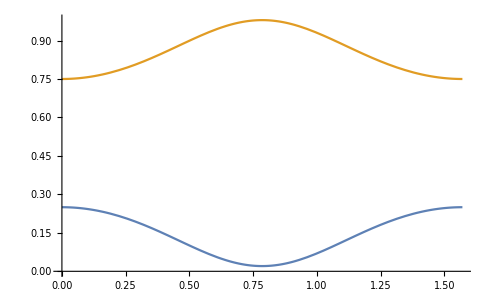

```mathematica
Plot[{R/.n1->1/.n2->2/.n3->3, T/.n1->1/.n2->2/.n3->3},{ω,0, Pi/2}]
```

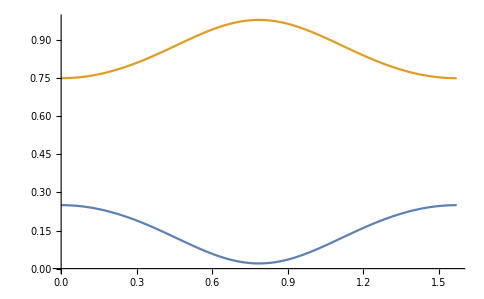

```mathematica
Plot[{R/.n1->3/.n2->2/.n3->1, T/.n1->3/.n2->2/.n3->1},{ω,0, Pi/2}]
```

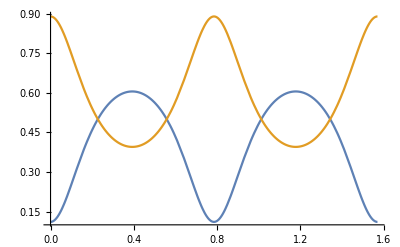

```mathematica
Plot[{R/.n1->2/.n2->4/.n3->1, T/.n1->2/.n2->4/.n3->1},{ω,0, Pi/2}]
```

```mathematica
Solve[R==0,d]
```

{}